```mathematica
(*1. Selected project, created a directory and submited it to github.*)
```

```mathematica
(* 2. Introduction
(a) The syntax of the Mathematica language *)
```

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y>y∧m ≠0⇒n⩾̸m
```

∀_x∃_y x⊗y>y&&m≠0⇒n⩾̸m

```mathematica
FullForm[%]
```

And[ForAll[x,Exists[y,Greater[CircleTimes[x,y],y]]],DoubleRightArrow[Unequal[m,0],NotGreaterSlantEqual[n,m]]]

```mathematica
{x -> #^2 &, (x -> #^2)&, x -> (#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a×a×a×b×b×c
```

a^3 b^2 c

```mathematica
∫k[x]ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x]b[x]ⅆx +c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s+n
```

n+Zeta[s]

```mathematica
(*(b)The meaning of Expressions*)
```

```mathematica
(*meaning of             f meaning ofx,y...                 examples
Function                arguments or parameters              Sin[x],f[x,y]
Command                  arguments or parameters            Expand[(x+1)^2]
Operator                  operands                            x+y,a=b
Head                        elements                         {a,b,c}
Objecttype                  contents                      RGBColor[r,g,b]*)
```

```mathematica
(*(c)The Four Kinds of Bracketing in Mathematica*)
```

```mathematica
(*(term) parentheses for grouping
   f[x] square brackets for functions
  {a,b,c} curly braces for lists
  v[[i]] double brackets for indexing (Part[v,i])
 When the expressions you type in are complicated,it is often a good idea to put extra space inside each set of brackets.This makes it somewhat easier for you to see matching pairs of brackets.*)
```

```mathematica
(*(d) Use Brackets and Braces Correctly: *)
(*You use parentheses in Mathematica for grouping expressions and to determine the precedence of operations:*)
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
(*A list in Mathematica is represented by braces and is a collection of items referred to as elements.*)
(*Create a List of the first five positive integers:*)
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3x==12,√(9+y),"hello"}
```

```mathematica
{1,b,2,3,3 x==12,√(9+y),"hello"}
(*Lists can contain other lists to create nested lists:*)
{1,1,{3,4,5},{3,2}}
```

{1,b,2,3,3 x==12,√(9+y),hello}

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets are used in Mathematica to enclose the arguments of functions.*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
(*Mathematica uses double square brackets as the short form for the Part function,which is used to get parts of lists:*)
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

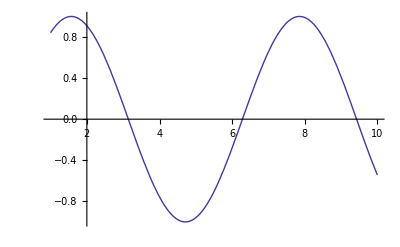

```mathematica
Plot[Sin[x],{x,1,10}]
```

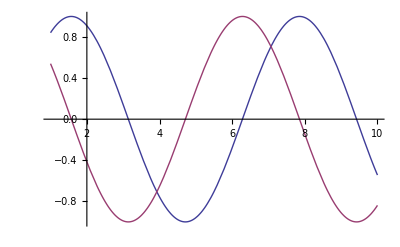

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*All bracketing characters must be balanced for Mathematica to evaluate an expression.When a bracketing character is unbalanced,the Mathematica front end colors it purple and attempting to evaluate the expression produces an error*)
```

```mathematica
(* 3. Symbolic Analysis *)
(*(a) Symbolic Computation:*)
```

```mathematica
3+62-1
```

64

```mathematica
3x-x+2
```

2+2 x

```mathematica
-1+2x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4x^2
```

x-3 x^2

```mathematica
(*Mathematica rearranges and combines terms using the standard rules of algebra.*)
x y+2x^2y+y^2 x^2 - 2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x + 2 y +1)(x - 2)^2
```

```mathematica
(-2+x)^2 (1+x+2 y)
```

(-2+x)^2 (1+x+2 y)

```mathematica
(* Expand multiplies ou product and powers.*)
```

```mathematica
Expand[%]
(*Factor does the inverse of Expand*)
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801(4 n)!(1103 + 26390 n )/ (n! ^4 396^(4n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1 + x]^4
```

(1+x)^2

```mathematica
Log[1 + Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*(b) Values for Symbols"*)
1+2 x/.x->3
```

7

```mathematica
(* You can replace x with any expression. *)
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x -> 3+y
```

x→3+y

```mathematica
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
(*The replacement operator allows you to apply transformation rules to a particular expression.Sometimes,however,you will want to define transformation rules that should always be applied.For example,you might want to replace with whenever occurs.As discussed in "Defining Variables",you can do this by assigning the value to using.Once you have made the assignment,will always be replaced by,whenever it appears.*)
x = 3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1 +a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
x+5 -2x
```

6+a-2 (1+a)

```mathematica
(*Removes the value you assigned to x.*)
x=.
```

```mathematica
x+5-2x
```

5-x

```mathematica
t = 1 + x^2
```

1+x^2

```mathematica
(*This finds the value of,and then replaces by in it.*)
```

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5 a
```

1+25 a^2

```mathematica
(*Finds the value of t when x is replaced by Pi, and then evaluates the result numerically*)
```

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
(*(c) Transforming Algebraic Expressions: *)
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
(*Factor recovers the original form. *)
```

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10 - 1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[%]
```

-1+x^10

```mathematica
(*(d)Simplifying Algebraic Expressions: *)
```

```mathematica
(*Simplify[expr] try to find the simplest form of expr by applying various standard algebraic transformations
FullSimplify[expr] try to find the simplest form by applying a wide range of transformations*)
```

```mathematica
Simplify[x^2 + 2 x +1]
```

(1+x)^2

```mathematica
Simplify[ x^10 -1]
```

-1+x^10

```mathematica
Integrate[1/(x^4 - 1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
(*For fairly small expressions,FullSimplify will often succeed in making some remarkable simplifications.But for larger expressions,it can become unmanageably slow.The reason for this is that to do its job,FullSimplify effectively has to try combining every part of an expression with every other,and for large expressions the number of cases that it has to consider can be astronomically large.Simplify also has a difficult task to do,but it is set up to avoid some of the most time-consuming transformations that are tried by FullSimplify.For simple algebraic calculations,therefore,you may often find it convenient to apply Simplify quite routinely to your results.*)
```

```mathematica
(*4.Calculus*)
(* (a) Differentiation: *)
```